# Initialization strategies for Deep Neural Networks

In this computational essay, we explore how different initialization strategies for neural networks can lead to vanishing activations as we do forward propagation.

Author Name, Jun. 24,  2018

We conduct an exploration of how activations diminish as the network depth increases, provided the initialization strategy of the network is inappropriate. We have to make several important and subtle choices when we attempt to train Deep Neural networks, and the rate of convergence of such a neural network can greatly depend on the initial conditions of the network as well.

## Forward propagation in neural networks

A typical deep neural network can be imagine as a series of matrix multiplications. Neural networks are trained by minimizing a loss function by changing the weights of the neural network. The gradient of a network always points in the direction of steepest increase, and we have to calculate the gradient of the loss with respect to the weights and move in the opposite direction.

As propagation in a vanilla neural network is a series of matrix multiplications, it becomes obvious that if the outputs of the network tend to zero, the gradients do too. If we initialize several matrices as done below,  and draw from different distributions, we can see vanishing or exploding results of the matrix multiplication.

Always have code text as a lead-in to code that follows, to concisely indicate what it does:

```mathematica
Code 
(* Experiment with the Normal Distribution properties to see how the product result histogram explodes/vanishes. *)
```

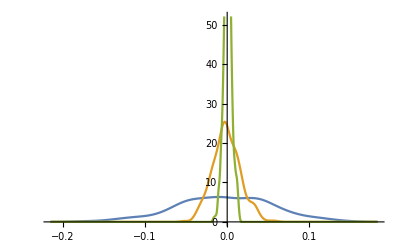

```mathematica
SeedRandom[91];
a = RandomVariate[NormalDistribution[0, 0.06], {20, 20}];
b = RandomVariate[NormalDistribution[0, 0.06], {20, 20}];c = RandomVariate[NormalDistribution[0, 0.06], {20, 20}];
h={Flatten[a], Flatten[a.b], Flatten[a.b.c]};
SmoothHistogram[h[[#]]&/@Range[3]]
```

## Section Header

Or show an example of application ...

Another way to start an exposition, or to expand on the basics, is to provide an example showing the application of the topic. The example might be something you arrive at by the end of the exposition, repeating that conclusion here is acceptable if it's reasonably self-contained. It might also be an example a problem scenario and the exposition explains a solution.

Always have code text as a lead-in to code that follows, to concisely indicate what it does:

```mathematica
Code (* demonstrate a specific application *)
```

## Section Header

Add more sections as needed to explain the topic....

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins

derivation

applications

common misunderstandings

recent developments

unanswered questions

## Further explorations

Name of a related topic for exploration

Name of another related topic for exploration (repeat as needed)

## Author contact information

emailaddress@author.com

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)